{I1→-(ⅈ I0)/(-ⅈ+Cc R ω),I2→(Cc I0 R ω)/(-ⅈ+Cc R ω)}

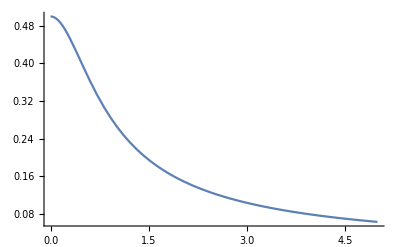

```mathematica
sol=Solve[{I0==I1+I2,I2 1/(I ω Cc)==R I1},{I1,I2}][[1]]

Plot[Abs[I1 R/.sol/.{I0 ->0.001,R->500,Cc->5 10^-12,ω->2 Pi f}],{f,0,500000000},PlotRange->All]
```

{I1→Function[{t},1/(1+Cc R)^2 Cc^2 R^2 ((ⅇ^(-t/(Cc R)) (-1+ⅇ^(1/(1000000000 Cc R))) I0 (1+Cc R)^2)/(Cc^2 R^2)+1/(Cc^2 R^2)ⅇ^(-t/(Cc R)) I0 (1+Cc R)^2 (-(ⅇ^(1/(1000000000 Cc R))-ⅇ^(1/(Cc R))) HeavisideTheta[-1+t] HeavisideTheta[-1/1000000000+t]+HeavisideTheta[1-t] (-ⅇ^(1/(1000000000 Cc R))+ⅇ^(1/(Cc R))+(ⅇ^(1/(1000000000 Cc R))-ⅇ^(t/(Cc R))) HeavisideTheta[-1/1000000000+t])-(-1+ⅇ^(1/(Cc R))) HeavisideTheta[-1+t] HeavisideTheta[t]-HeavisideTheta[1-t] (-1+ⅇ^(1/(Cc R))+HeavisideTheta[t]-ⅇ^(t/(Cc R)) HeavisideTheta[t])+HeavisideTheta[-1+t] ((ⅇ^(1/(1000000000 Cc R))-ⅇ^(t/(Cc R))) HeavisideTheta[-1/1000000000+t]+(-1+ⅇ^(t/(Cc R))) HeavisideTheta[t])))],I2→Function[{t},I0 HeavisidePi[1000000000 (-1/2000000000+t)]-1/(1+Cc R)^2 Cc^2 R^2 ((ⅇ^(-t/(Cc R)) (-1+ⅇ^(1/(1000000000 Cc R))) I0 (1+Cc R)^2)/(Cc^2 R^2)+1/(Cc^2 R^2)ⅇ^(-t/(Cc R)) I0 (1+Cc R)^2 (-(ⅇ^(1/(1000000000 Cc R))-ⅇ^(1/(Cc R))) HeavisideTheta[-1+t] HeavisideTheta[-1/1000000000+t]+HeavisideTheta[1-t] (-ⅇ^(1/(1000000000 Cc R))+ⅇ^(1/(Cc R))+(ⅇ^(1/(1000000000 Cc R))-ⅇ^(t/(Cc R))) HeavisideTheta[-1/1000000000+t])-(-1+ⅇ^(1/(Cc R))) HeavisideTheta[-1+t] HeavisideTheta[t]-HeavisideTheta[1-t] (-1+ⅇ^(1/(Cc R))+HeavisideTheta[t]-ⅇ^(t/(Cc R)) HeavisideTheta[t])+HeavisideTheta[-1+t] ((ⅇ^(1/(1000000000 Cc R))-ⅇ^(t/(Cc R))) HeavisideTheta[-1/1000000000+t]+(-1+ⅇ^(t/(Cc R))) HeavisideTheta[t])))]}

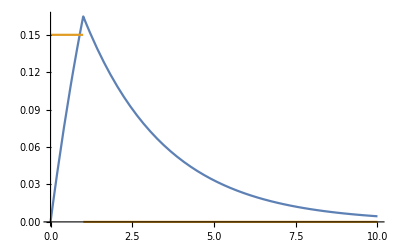

```mathematica
sol=DSolve[{I0 HeavisidePi[(t-1/2 10^-9)/10^-9]==I1[t]+I2[t],I2[t]/Cc==R I1'[t],I1[0]==0},{I1,I2},t][[1]]
Plot[{R I1[t 10^-9]/.sol/.{I0 ->0.001,R->500,Cc->5 10^-12},0.15(HeavisideTheta[t]-HeavisideTheta[t-1])},{t,0,10},PlotRange->All,AxesOrigin->{0,0}]
```

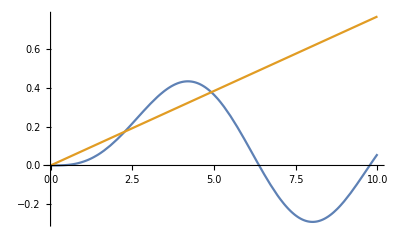

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[BesselJ[3,x]==x/13,x]

{x→2.26989}

```mathematica
(*Нахождение корней нелинейного уравнения*)

Plot[{BesselJ[3,x],1/13x},{x,0,10}]

Solve[BesselJ[3,x]==1/13x,x] (*Solve работает преимущественно для линейных уравниний, здесь не годится, выдает ошибку*)

FindRoot[BesselJ[3,x]==1/13x,{x,2}] (*FindRoot решает численными методами*)
```

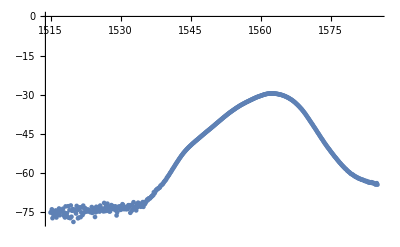

```mathematica
(*Импорт из файла*)

spec=Import["Data.xlsx",Path->NotebookDirectory[]][[1]];

(*или *)

SetDirectory["C:\\Program Files..."]
Import["Data.xlsx"][[1]];

ListPlot[spec]
```

Домашнее задание

1) Изучить еще раз операторы Part, Span
2) Найти аналитически сигнал снимаемый с фотодиода, если на фотодиод падает оптический импульс по форме являющимся равносторонним треугольником с основанием 2τ (τ - время возрастания интенсивности, τ - время убывания). Граничные условия периодические: через 10τ приходит новый импульс, т.е. все токи в контуре будут повторяться с периодом 10τ
	Уметь решать эту задачу как во временном, так и в частотном пространствах
	Как изменится измеряемый сигнал, если устремить Сс в бесконечность? Уметь объяснить и решить такой частный случай на бумажке в одну строчку
	Сигнал с нагрузочного сопротивления заводится на компаратор. Рассчитать уровень компаратора, при котором на выходе с него получается меандр со скважностью 2
	Решить обратную задачу. Известны параметры эквивалентной схемы и измеренный сигнал во временном пространстве (взять произвольную функцию с ограниченной областью ненулевых значений)
	Все параметры задачи известны кроме R. Рассудить из каких соображений необходимо выбирать нагрузочное сопротивление в эксперименте. Чем выбор ограничен сверху и снизу?
3) В файле “Data.xlsx” на листе “HomeWork. Pulse” представлена измеренная форма импульса на выходе из лазера. Известно, что PRR - 16.5 МГц, средняя мощность на выходе 19 мВт. Найти точно пиковую мощность импульса. 
	Учесть, что в выходном излучении присутствует доля непрерывного излучения
4) Аппроксимировать спектр из листа “Spectrum” гауссовым. Использовать FindFit, нарисовать одновременно и точки и аппроксимацию. Вывести вычисленные параметры аппроксимации.
	Геометрический смысл параметров аппроксимации. Уметь пересчитывать ширину гауссовой функции из любого параметра 1/e^2, 1/e, FWHM в любой.
5) Дан элемент, спектр отражения которого приведен на листе “HomeWork. VBG” (в процентах). Найти отраженный спектр “Spectrum” от данного элемента.
	Уметь проделывать процедуру в линейном и логарифмическом масштабах
	Процент отражения полной мощности
6) Изучить https://en.wikipedia.org/wiki/Finite_difference_coefficient . Составить оператор, который дифференцирует дискретную функцию с 1, 2 и 4 порядком точности. 
	Учесть различные коэффициенты дифференциалов на границе области определения функции
	Применить оператор, например, к “Spectrum”. Возможно, здесь пригодится функция ListConvolve
7) На листе Phase в первых двух столбцах представлены измеренные экспериментальные точки некоторой зависимости. В конечном счете необходимо взять производную от этой функции. Способ взятия можете придумать сами. Можете сделать следующие шаги:
	Обработать точки с одинаковыми аргументами
	Заменить сетку дискретизации на равномерную
	Применить фильтр/фильтры к массиву точек guide/DataTransformsAndSmoothing
	Взять численно производную